## Axion off-diagonal couplings to quarks and leptons

Goal: 
	Data analysis
	
Input: 
	output/yukawa_quark.m
	output/yukawa_lepton.m
	
Output:
	Figure 4
	Figure 5

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[StringDrop[NotebookDirectory[],-4]]
```

H:\2_Projects\physics\5d_flavourful_axion

```mathematica
<<"WarpFlavourAxion`"
```

FermionAxionOverlap::shdw: Symbol FermionAxionOverlap appears in multiple contexts {WarpFlavourAxion`,Global`}; definitions in context WarpFlavourAxion` may shadow or be shadowed by other definitions.

### Import Data

```mathematica
quarkData = <<"output/yukawa_quark.m";
Print["Number of Yu Yd 3x3 matrix pairs"]
Dimensions[quarkData]
```

Number of Yu Yd 3x3 matrix pairs

{1321,2,3,3}

```mathematica
leptonData = <<"output/yukawa_lepton.m";
Print["Number of Yn Ye 3x3 matrix pairs (normal hierarchy)"]
Dimensions[leptonData[[1]]]
Print["Number of Yn Ye 3x3 matrix pairs (inverted hierarchy)"]
Dimensions[leptonData[[2]]]
```

Number of Yn Ye 3x3 matrix pairs (normal hierarchy)

{4330,2,3,3}

Number of Yn Ye 3x3 matrix pairs (inverted hierarchy)

{}

### Find the axion - fermions off-diagonal couplings

#### Loading necessary data

```mathematica
(* Import cL, cR calculated above *)
```

```mathematica
{cMArray,cuData,cdData,clNHData}=<<"output/cLcR03.m";
```

```mathematica
Dimensions/@{cuData,cdData,clNHData}
```

{{1321,26,3,2},{1321,26,3,2},{4330,26,3,2}}

```mathematica
(* Get A matrices from yu, yd data *)
```

```mathematica
quarkAData = Table[
yu = quarkData[[i, 1]]; yd = quarkData[[i,2]];myu=Minors[quarkData[[i, 1]]];myd=Minors[quarkData[[i, 2]]];
QuarkAMatrices[yu, yd, myu, myd]
,{i,Length[quarkData]}
];//AbsoluteTiming
Clear[yu,yd,myu,myd]
Dimensions[quarkAData]
```

{1.18904,Null}

{1321,4,3,3}

```mathematica
leptonADataNH = Table[
yn = leptonData[[1]][[i, 1]]; ye = leptonData[[1]][[i,2]];myn=Minors[yn];mye=Minors[ye];
LeptonAMatrices[yn, ye, myn, mye,1]
,{i,Length[leptonData[[1]]]}
];//AbsoluteTiming
Clear[yn,ye,myn,mye]
Dimensions[leptonADataNH]
```

{1.83779,Null}

{4330,2,3,3}

```mathematica
(* 
leptonADataIH = Table[
yn = leptonData[[2]][[i, 1]]; ye = leptonData[[2]][[i,2]];myn=Minors[yn];mye=Minors[ye];
LeptonAMatrices[yn, ye, myn, mye,2]
,{i,Length[leptonData[[2]]]}
];//AbsoluteTiming
Clear[yn,ye,myn,mye]
Dimensions[leptonADataIH]
*)
```

```mathematica
colors=ColorData[97,"ColorList"];
```

```mathematica
fvmin = 14.7;fvmax=17.7;
cvmin=fvmin-20.7;cvmax=fvmax-20.7;
cmmin=-4;cmmax = 4;
```

#### Up Quark

```mathematica
(* Change these data to obtain down or lepton figures *)
```

```mathematica
data=cuData;
```

```mathematica
AData = quarkAData;
```

```mathematica
ΔArray = {7, 9, 11};
```

```mathematica
(* Be cautious editting the rest *)
```

```mathematica
(* cV *)
```

```mathematica
With[
{kMax = Dimensions[data][[1]], cmTotal =Dimensions[data][[2]],Δ=ΔArray[[2]],α=1/2},
output=Table[
α AData[[k,2]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, 2]] ,Δ],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,2]] ] -
(1-α) AData[[k,1]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, 1]] ,Δ],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,1]] ],
{k,kMax},{cmpt,cmTotal}]
];
```

```mathematica
y12= Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,1,2]] ]]],
{cmpt,Dimensions[data][[2]]}
];
y13= Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,1,3]] ]]],
{cmpt,Dimensions[data][[2]]}
];
y23= Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,2,3]] ]]],
{cmpt,Dimensions[data][[2]]}
];
```

```mathematica
With[
{kMax = Dimensions[data][[1]], cmTotal =Dimensions[data][[2]],α=1/2},
outputDelta=Table[
α AData[[k,2]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, 2]],Δ ],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,2]] ]- 
(1-α) AData[[k,1]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, 1]] ,Δ],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,1]] ],
{Δ,ΔArray},{k,kMax},{cmpt,cmTotal}]
];
```

```mathematica
y12vDelta =Table[
 Mean[Log10/@Abs[outputDelta[[Δidx,All,cmpt,1,2]]]],
{Δidx,3},{cmpt,Dimensions[data][[2]]}
];
y13vDelta =Table[
 Mean[Log10/@Abs[outputDelta[[Δidx,All,cmpt,1,3]]]],
{Δidx,3},{cmpt,Dimensions[data][[2]]}
];
y23vDelta =Table[
 Mean[Log10/@Abs[outputDelta[[Δidx,All,cmpt,2,3]]]],
{Δidx,3},{cmpt,Dimensions[data][[2]]}
];
```

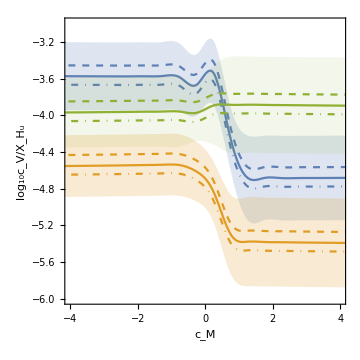

```mathematica
Show[
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,PlotRange->{{cmmin,cmmax},{cvmin,cvmax}},ImageSize->Medium,FrameLabel->{"c_M","log_10c_V/X_H_u"},AspectRatio->1,
PlotStyle->{colors[[1]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[1]]]
]& @ y12,
ListPlot[{{cMArray,#1[[1]]}//Transpose,{cMArray,#1[[3]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{{colors[[#2]],Dashed},{colors[[#2]],DotDashed}}
]&[y12vDelta,1],
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[2]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[2]]]
]& @ y13,
ListPlot[{{cMArray,#1[[1]]}//Transpose,{cMArray,#1[[3]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{{colors[[#2]],Dashed},{colors[[#2]],DotDashed}}
]&[y13vDelta,2],
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[3]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.1],colors[[3]]]
]& @ y23,
ListPlot[{{cMArray,#1[[1]]}//Transpose,{cMArray,#1[[3]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{{colors[[#2]],Dashed},{colors[[#2]],DotDashed}}
]&[y23vDelta,3]
]
```

```mathematica
Export["Figures/up_cV.pdf",%]
```

Figures/up_cV.pdf

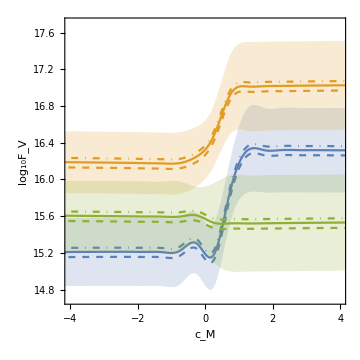

```mathematica
With[{σ0 =0.1,g=1,Mpl=1.22 10^19,zir=10^8,Δ=ΔArray[[2]]},
Clear[Fa];Fa[Δ_]:=Mpl/zir σ0/Sqrt[Δ-1];
Show[
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotRange->{{cmmin,cmmax},{fvmin,fvmax}},ImageSize->Medium,FrameLabel->{"c_M","log_10F_V"},AspectRatio->1,
PlotStyle->{colors[[1]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[1]]]
]& @ ( ({Log10[Fa[Δ]/(g^2 σ0^2)],0}-#)&/@y12),
ListPlot[{cMArray,#1[[1]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],Dashed}
]&[ (Log10[Fa[ΔArray[[1]]]/(g^2 σ0^2)]-y12vDelta),1],
ListPlot[{cMArray,#1[[3]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],DotDashed}
]&[ (Log10[Fa[ΔArray[[3]]]/(g^2 σ0^2)]-y12vDelta),1],
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[2]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[2]]]
]& @  ( ({Log10[Fa[Δ]/(g^2 σ0^2)],0}-#)&/@y13),
ListPlot[{cMArray,#1[[1]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],Dashed}
]&[ (Log10[Fa[ΔArray[[1]]]/(g^2 σ0^2)]-y13vDelta),2],
ListPlot[{cMArray,#1[[3]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],DotDashed}
]&[ (Log10[Fa[ΔArray[[3]]]/(g^2 σ0^2)]-y13vDelta),2],
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[3]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[3]]]
]& @ ( ({Log10[Fa[Δ]/(g^2 σ0^2)],0}-#)&/@y23),
ListPlot[{cMArray,#1[[1]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],Dashed}
]&[ (Log10[Fa[ΔArray[[1]]]/(g^2 σ0^2)]-y23vDelta),3],
ListPlot[{cMArray,#1[[3]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],DotDashed}
]&[ (Log10[Fa[ΔArray[[3]]]/(g^2 σ0^2)]-y23vDelta),3],
ListPlot[Table[{i,12},{i,cMArray}],Joined->True,PlotStyle->{Opacity[0.2],colors[[5]]},
Filling->Bottom,FillingStyle->Directive[Opacity[0.2],colors[[5]]]]
]
]
```

```mathematica
Export["Figures/up_FV.pdf",%]
```

Figures/up_FV.pdf

```mathematica
(* cA *)
```

```mathematica
With[
{kMax = Dimensions[data][[1]], cmTotal =Dimensions[data][[2]],Δ=ΔArray[[2]],α=1/2},
output=Table[
α AData[[k,2]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, 2]] ,Δ],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,2]] ] +
(1-α) AData[[k,1]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, 1]] ,Δ],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,1]] ],
{k,kMax},{cmpt,cmTotal}]
];
```

```mathematica
y12= Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,1,2]] ]]],
{cmpt,Dimensions[data][[2]]}
];
y13= Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,1,3]] ]]],
{cmpt,Dimensions[data][[2]]}
];
y23= Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,2,3]] ]]],
{cmpt,Dimensions[data][[2]]}
];
```

```mathematica
With[
{kMax = Dimensions[data][[1]], cmTotal =Dimensions[data][[2]],α=1/2},
outputDelta=Table[
α AData[[k,2]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, 2]],Δ ],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,2]] ]- 
(1-α) AData[[k,1]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, 1]] ,Δ],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,1]] ],
{Δ,ΔArray},{k,kMax},{cmpt,cmTotal}]
];
```

```mathematica
y12vDelta =Table[
 Mean[Log10/@Abs[outputDelta[[Δidx,All,cmpt,1,2]]]],
{Δidx,3},{cmpt,Dimensions[data][[2]]}
];
y13vDelta =Table[
 Mean[Log10/@Abs[outputDelta[[Δidx,All,cmpt,1,3]]]],
{Δidx,3},{cmpt,Dimensions[data][[2]]}
];
y23vDelta =Table[
 Mean[Log10/@Abs[outputDelta[[Δidx,All,cmpt,2,3]]]],
{Δidx,3},{cmpt,Dimensions[data][[2]]}
];
```

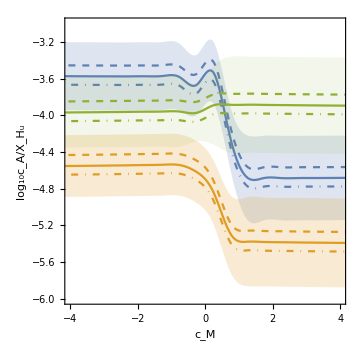

```mathematica
Show[
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,PlotRange->{{cmmin,cmmax},{cvmin,cvmax}},ImageSize->Medium,FrameLabel->{"c_M","log_10c_A/X_H_u"},AspectRatio->1,
PlotStyle->{colors[[1]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[1]]]
]& @ y12,
ListPlot[{{cMArray,#1[[1]]}//Transpose,{cMArray,#1[[3]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{{colors[[#2]],Dashed},{colors[[#2]],DotDashed}}
]&[y12vDelta,1],
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[2]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[2]]]
]& @ y13,
ListPlot[{{cMArray,#1[[1]]}//Transpose,{cMArray,#1[[3]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{{colors[[#2]],Dashed},{colors[[#2]],DotDashed}}
]&[y13vDelta,2],
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[3]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.1],colors[[3]]]
]& @ y23,
ListPlot[{{cMArray,#1[[1]]}//Transpose,{cMArray,#1[[3]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{{colors[[#2]],Dashed},{colors[[#2]],DotDashed}}
]&[y23vDelta,3]
]
```

```mathematica
Export["Figures/up_cA.pdf",%]
```

Figures/up_cA.pdf

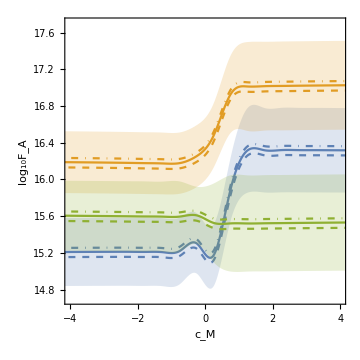

```mathematica
With[{σ0 =0.1,g=1,Mpl=1.22 10^19,zir=10^8,Δ=ΔArray[[2]]},
Clear[Fa];Fa[Δ_]:=Mpl/zir σ0/Sqrt[Δ-1];
Show[
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotRange->{{cmmin,cmmax},{fvmin,fvmax}},ImageSize->Medium,FrameLabel->{"c_M","log_10F_A"},AspectRatio->1,
PlotStyle->{colors[[1]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[1]]]
]& @ ( ({Log10[Fa[Δ]/(g^2 σ0^2)],0}-#)&/@y12),
ListPlot[{cMArray,#1[[1]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],Dashed}
]&[ (Log10[Fa[ΔArray[[1]]]/(g^2 σ0^2)]-y12vDelta),1],
ListPlot[{cMArray,#1[[3]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],DotDashed}
]&[ (Log10[Fa[ΔArray[[3]]]/(g^2 σ0^2)]-y12vDelta),1],
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[2]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[2]]]
]& @  ( ({Log10[Fa[Δ]/(g^2 σ0^2)],0}-#)&/@y13),
ListPlot[{cMArray,#1[[1]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],Dashed}
]&[ (Log10[Fa[ΔArray[[1]]]/(g^2 σ0^2)]-y13vDelta),2],
ListPlot[{cMArray,#1[[3]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],DotDashed}
]&[ (Log10[Fa[ΔArray[[3]]]/(g^2 σ0^2)]-y13vDelta),2],
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[3]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[3]]]
]& @ ( ({Log10[Fa[Δ]/(g^2 σ0^2)],0}-#)&/@y23),
ListPlot[{cMArray,#1[[1]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],Dashed}
]&[ (Log10[Fa[ΔArray[[1]]]/(g^2 σ0^2)]-y23vDelta),3],
ListPlot[{cMArray,#1[[3]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],DotDashed}
]&[ (Log10[Fa[ΔArray[[3]]]/(g^2 σ0^2)]-y23vDelta),3],
ListPlot[Table[{i,12},{i,cMArray}],Joined->True,PlotStyle->{Opacity[0.2],colors[[5]]},
Filling->Bottom,FillingStyle->Directive[Opacity[0.2],colors[[5]]]]
]
]
```

```mathematica
Export["Figures/up_FA.pdf",%]
```

Figures/up_FA.pdf

#### Down Quark

```mathematica
(* Change these data to obtain down or lepton figures *)
```

```mathematica
data=cdData;
```

```mathematica
AData = quarkAData;
```

```mathematica
ΔArray = {7, 9, 11};
```

```mathematica
(* Be cautious editting the rest *)
```

```mathematica
(* cV *)
```

```mathematica
With[
{kMax = Dimensions[data][[1]], cmTotal =Dimensions[data][[2]],Δ=ΔArray[[2]],α=1/2},
output=Table[
α AData[[k,4]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, 2]] ,Δ],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,4]] ] -
(1-α) AData[[k,3]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, 1]] ,Δ],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,3]] ],
{k,kMax},{cmpt,cmTotal}]
];
```

```mathematica
y12= Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,1,2]] ]]],
{cmpt,Dimensions[data][[2]]}
];
y13= Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,1,3]] ]]],
{cmpt,Dimensions[data][[2]]}
];
y23= Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,2,3]] ]]],
{cmpt,Dimensions[data][[2]]}
];
```

```mathematica
With[
{kMax = Dimensions[data][[1]], cmTotal =Dimensions[data][[2]],α=1/2},
outputDelta=Table[
α AData[[k,4]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, 2]],Δ ],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,4]] ]- 
(1-α) AData[[k,3]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, 1]] ,Δ],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,3]] ],
{Δ,ΔArray},{k,kMax},{cmpt,cmTotal}]
];
```

```mathematica
y12vDelta =Table[
 Mean[Log10/@Abs[outputDelta[[Δidx,All,cmpt,1,2]]]],
{Δidx,3},{cmpt,Dimensions[data][[2]]}
];
y13vDelta =Table[
 Mean[Log10/@Abs[outputDelta[[Δidx,All,cmpt,1,3]]]],
{Δidx,3},{cmpt,Dimensions[data][[2]]}
];
y23vDelta =Table[
 Mean[Log10/@Abs[outputDelta[[Δidx,All,cmpt,2,3]]]],
{Δidx,3},{cmpt,Dimensions[data][[2]]}
];
```

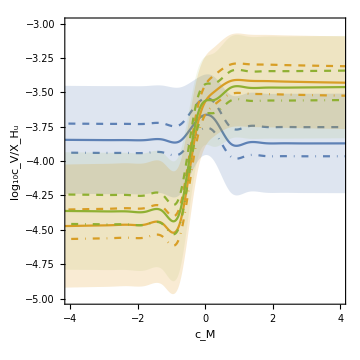

```mathematica
Show[
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotRange->{{cmmin,cmmax},{-5,-3}},ImageSize->Medium,FrameLabel->{"c_M","log_10c_V/X_H_u"},AspectRatio->1,
PlotStyle->{colors[[1]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[1]]]
]& @ y12,
ListPlot[{{cMArray,#1[[1]]}//Transpose,{cMArray,#1[[3]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{{colors[[#2]],Dashed},{colors[[#2]],DotDashed}}
]&[y12vDelta,1],
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[2]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[2]]]
]& @ y13,
ListPlot[{{cMArray,#1[[1]]}//Transpose,{cMArray,#1[[3]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{{colors[[#2]],Dashed},{colors[[#2]],DotDashed}}
]&[y13vDelta,2],
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[3]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.1],colors[[3]]]
]& @ y23,
ListPlot[{{cMArray,#1[[1]]}//Transpose,{cMArray,#1[[3]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{{colors[[#2]],Dashed},{colors[[#2]],DotDashed}}
]&[y23vDelta,3]
]
```

```mathematica
Export["Figures/down_cV.pdf",%]
```

Figures/down_cV.pdf

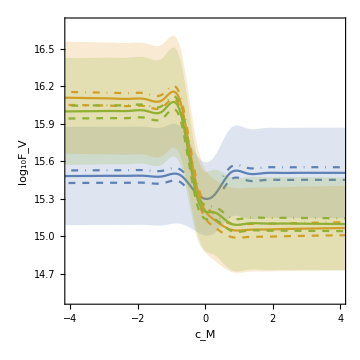

```mathematica
With[{σ0 =0.1,g=1,Mpl=1.22 10^19,zir=10^8,Δ=ΔArray[[2]]},
Clear[Fa];Fa[Δ_]:=Mpl/zir σ0/Sqrt[Δ-1];
Show[
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotRange->{{cmmin,cmmax},{14.5,16.7}},ImageSize->Medium,FrameLabel->{"c_M","log_10F_V"},AspectRatio->1,
PlotStyle->{colors[[1]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[1]]]
]& @ ( ({Log10[Fa[Δ]/(g^2 σ0^2)],0}-#)&/@y12),
ListPlot[{cMArray,#1[[1]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],Dashed}
]&[ (Log10[Fa[ΔArray[[1]]]/(g^2 σ0^2)]-y12vDelta),1],
ListPlot[{cMArray,#1[[3]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],DotDashed}
]&[ (Log10[Fa[ΔArray[[3]]]/(g^2 σ0^2)]-y12vDelta),1],
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[2]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[2]]]
]& @  ( ({Log10[Fa[Δ]/(g^2 σ0^2)],0}-#)&/@y13),
ListPlot[{cMArray,#1[[1]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],Dashed}
]&[ (Log10[Fa[ΔArray[[1]]]/(g^2 σ0^2)]-y13vDelta),2],
ListPlot[{cMArray,#1[[3]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],DotDashed}
]&[ (Log10[Fa[ΔArray[[3]]]/(g^2 σ0^2)]-y13vDelta),2],
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[3]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[3]]]
]& @ ( ({Log10[Fa[Δ]/(g^2 σ0^2)],0}-#)&/@y23),
ListPlot[{cMArray,#1[[1]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],Dashed}
]&[ (Log10[Fa[ΔArray[[1]]]/(g^2 σ0^2)]-y23vDelta),3],
ListPlot[{cMArray,#1[[3]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],DotDashed}
]&[ (Log10[Fa[ΔArray[[3]]]/(g^2 σ0^2)]-y23vDelta),3],
ListPlot[Table[{i,12},{i,cMArray}],Joined->True,PlotStyle->{Opacity[0.2],colors[[5]]},
Filling->Bottom,FillingStyle->Directive[Opacity[0.2],colors[[5]]]]
]
]
```

```mathematica
Export["Figures/down_FV.pdf",%]
```

Figures/down_FV.pdf

```mathematica
(* cA *)
```

```mathematica
With[
{kMax = Dimensions[data][[1]], cmTotal =Dimensions[data][[2]],Δ=ΔArray[[2]],α=1/2},
output=Table[
α AData[[k,4]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, 2]] ,Δ],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,4]] ] +
(1-α) AData[[k,3]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, 1]] ,Δ],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,3]] ],
{k,kMax},{cmpt,cmTotal}]
];
```

```mathematica
y12= Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,1,2]] ]]],
{cmpt,Dimensions[data][[2]]}
];
y13= Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,1,3]] ]]],
{cmpt,Dimensions[data][[2]]}
];
y23= Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,2,3]] ]]],
{cmpt,Dimensions[data][[2]]}
];
```

```mathematica
With[
{kMax = Dimensions[data][[1]], cmTotal =Dimensions[data][[2]],α=1/2},
outputDelta=Table[
α AData[[k,4]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, 2]],Δ ],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,4]] ]- 
(1-α) AData[[k,3]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, 1]] ,Δ],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,3]] ],
{Δ,ΔArray},{k,kMax},{cmpt,cmTotal}]
];
```

```mathematica
y12vDelta =Table[
 Mean[Log10/@Abs[outputDelta[[Δidx,All,cmpt,1,2]]]],
{Δidx,3},{cmpt,Dimensions[data][[2]]}
];
y13vDelta =Table[
 Mean[Log10/@Abs[outputDelta[[Δidx,All,cmpt,1,3]]]],
{Δidx,3},{cmpt,Dimensions[data][[2]]}
];
y23vDelta =Table[
 Mean[Log10/@Abs[outputDelta[[Δidx,All,cmpt,2,3]]]],
{Δidx,3},{cmpt,Dimensions[data][[2]]}
];
```

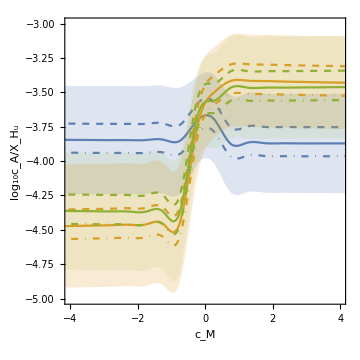

```mathematica
Show[
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,PlotRange->{{cmmin,cmmax},{-5,-3}},ImageSize->Medium,FrameLabel->{"c_M","log_10c_A/X_H_u"},AspectRatio->1,
PlotStyle->{colors[[1]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[1]]]
]& @ y12,
ListPlot[{{cMArray,#1[[1]]}//Transpose,{cMArray,#1[[3]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{{colors[[#2]],Dashed},{colors[[#2]],DotDashed}}
]&[y12vDelta,1],
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[2]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[2]]]
]& @ y13,
ListPlot[{{cMArray,#1[[1]]}//Transpose,{cMArray,#1[[3]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{{colors[[#2]],Dashed},{colors[[#2]],DotDashed}}
]&[y13vDelta,2],
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[3]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.1],colors[[3]]]
]& @ y23,
ListPlot[{{cMArray,#1[[1]]}//Transpose,{cMArray,#1[[3]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{{colors[[#2]],Dashed},{colors[[#2]],DotDashed}}
]&[y23vDelta,3]
]
```

```mathematica
Export["Figures/down_cA.pdf",%]
```

Figures/down_cA.pdf

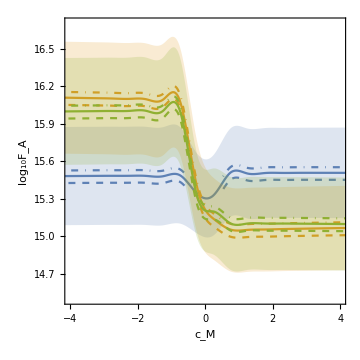

```mathematica
With[{σ0 =0.1,g=1,Mpl=1.22 10^19,zir=10^8,Δ=ΔArray[[2]]},
Clear[Fa];Fa[Δ_]:=Mpl/zir σ0/Sqrt[Δ-1];
Show[
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotRange->{{cmmin,cmmax},{14.5,16.7}},ImageSize->Medium,FrameLabel->{"c_M","log_10F_A"},AspectRatio->1,
PlotStyle->{colors[[1]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[1]]]
]& @ ( ({Log10[Fa[Δ]/(g^2 σ0^2)],0}-#)&/@y12),
ListPlot[{cMArray,#1[[1]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],Dashed}
]&[ (Log10[Fa[ΔArray[[1]]]/(g^2 σ0^2)]-y12vDelta),1],
ListPlot[{cMArray,#1[[3]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],DotDashed}
]&[ (Log10[Fa[ΔArray[[3]]]/(g^2 σ0^2)]-y12vDelta),1],
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[2]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[2]]]
]& @  ( ({Log10[Fa[Δ]/(g^2 σ0^2)],0}-#)&/@y13),
ListPlot[{cMArray,#1[[1]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],Dashed}
]&[ (Log10[Fa[ΔArray[[1]]]/(g^2 σ0^2)]-y13vDelta),2],
ListPlot[{cMArray,#1[[3]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],DotDashed}
]&[ (Log10[Fa[ΔArray[[3]]]/(g^2 σ0^2)]-y13vDelta),2],
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[3]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[3]]]
]& @ ( ({Log10[Fa[Δ]/(g^2 σ0^2)],0}-#)&/@y23),
ListPlot[{cMArray,#1[[1]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],Dashed}
]&[ (Log10[Fa[ΔArray[[1]]]/(g^2 σ0^2)]-y23vDelta),3],
ListPlot[{cMArray,#1[[3]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],DotDashed}
]&[ (Log10[Fa[ΔArray[[3]]]/(g^2 σ0^2)]-y23vDelta),3],
ListPlot[Table[{i,12},{i,cMArray}],Joined->True,PlotStyle->{Opacity[0.2],colors[[5]]},
Filling->Bottom,FillingStyle->Directive[Opacity[0.2],colors[[5]]]]
]
]
```

```mathematica
Export["Figures/down_FA.pdf",%]
```

Figures/down_FA.pdf

#### Lepton Normal Hierarchy

```mathematica
(* Change these data to obtain down or lepton figures *)
```

```mathematica
data=clNHData;
```

```mathematica
AData = leptonADataNH;
```

```mathematica
ΔArray = {7, 9, 11};
```

```mathematica
(* Be cautious editting the rest *)
```

```mathematica
(* cV *)
```

```mathematica
With[
{kMax = Dimensions[data][[1]], cmTotal =Dimensions[data][[2]],Δ=ΔArray[[2]],α=1/2},
output=Table[
α AData[[k,2]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, 2]] ,Δ],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,2]] ] -
(1-α) AData[[k,1]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, 1]] ,Δ],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,1]] ],
{k,kMax},{cmpt,cmTotal}]
];
```

```mathematica
y12= Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,1,2]] ]]],
{cmpt,Dimensions[data][[2]]}
];
y13= Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,1,3]] ]]],
{cmpt,Dimensions[data][[2]]}
];
y23= Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,2,3]] ]]],
{cmpt,Dimensions[data][[2]]}
];
```

```mathematica
With[
{kMax = Dimensions[data][[1]], cmTotal =Dimensions[data][[2]],α=1/2},
outputDelta=Table[
α AData[[k,2]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, 2]],Δ ],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,2]] ]- 
(1-α) AData[[k,1]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, 1]] ,Δ],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,1]] ],
{Δ,ΔArray},{k,kMax},{cmpt,cmTotal}]
];
```

```mathematica
y12vDelta =Table[
 Mean[Log10/@Abs[outputDelta[[Δidx,All,cmpt,1,2]]]],
{Δidx,3},{cmpt,Dimensions[data][[2]]}
];
y13vDelta =Table[
 Mean[Log10/@Abs[outputDelta[[Δidx,All,cmpt,1,3]]]],
{Δidx,3},{cmpt,Dimensions[data][[2]]}
];
y23vDelta =Table[
 Mean[Log10/@Abs[outputDelta[[Δidx,All,cmpt,2,3]]]],
{Δidx,3},{cmpt,Dimensions[data][[2]]}
];
```

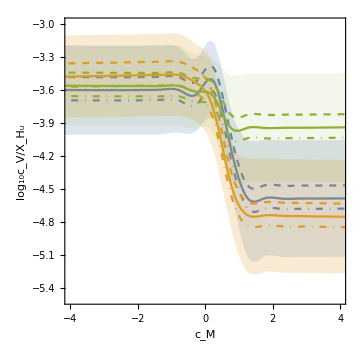

```mathematica
Show[
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,PlotRange->{{cmmin,cmmax},{-5.5,-3.0}},ImageSize->Medium,FrameLabel->{"c_M","log_10c_V/X_H_u"},AspectRatio->1,
PlotStyle->{colors[[1]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[1]]]
]& @ y12,
ListPlot[{{cMArray,#1[[1]]}//Transpose,{cMArray,#1[[3]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{{colors[[#2]],Dashed},{colors[[#2]],DotDashed}}
]&[y12vDelta,1],
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[2]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[2]]]
]& @ y13,
ListPlot[{{cMArray,#1[[1]]}//Transpose,{cMArray,#1[[3]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{{colors[[#2]],Dashed},{colors[[#2]],DotDashed}}
]&[y13vDelta,2],
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[3]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.1],colors[[3]]]
]& @ y23,
ListPlot[{{cMArray,#1[[1]]}//Transpose,{cMArray,#1[[3]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{{colors[[#2]],Dashed},{colors[[#2]],DotDashed}}
]&[y23vDelta,3]
]
```

```mathematica
Export["Figures/lepton_nh_cV.pdf",%]
```

Figures/lepton_nh_cV.pdf

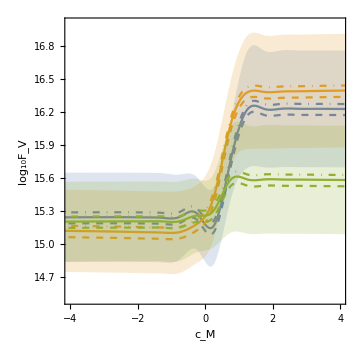

```mathematica
With[{σ0 =0.1,g=1,Mpl=1.22 10^19,zir=10^8,Δ=ΔArray[[2]]},
Clear[Fa];Fa[Δ_]:=Mpl/zir σ0/Sqrt[Δ-1];
Show[
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotRange->{{cmmin,cmmax},{14.5,17}},ImageSize->Medium,FrameLabel->{"c_M","log_10F_V"},AspectRatio->1,
PlotStyle->{colors[[1]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[1]]]
]& @ ( ({Log10[Fa[Δ]/(g^2 σ0^2)],0}-#)&/@y12),
ListPlot[{cMArray,#1[[1]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],Dashed}
]&[ (Log10[Fa[ΔArray[[1]]]/(g^2 σ0^2)]-y12vDelta),1],
ListPlot[{cMArray,#1[[3]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],DotDashed}
]&[ (Log10[Fa[ΔArray[[3]]]/(g^2 σ0^2)]-y12vDelta),1],
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[2]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[2]]]
]& @  ( ({Log10[Fa[Δ]/(g^2 σ0^2)],0}-#)&/@y13),
ListPlot[{cMArray,#1[[1]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],Dashed}
]&[ (Log10[Fa[ΔArray[[1]]]/(g^2 σ0^2)]-y13vDelta),2],
ListPlot[{cMArray,#1[[3]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],DotDashed}
]&[ (Log10[Fa[ΔArray[[3]]]/(g^2 σ0^2)]-y13vDelta),2],
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[3]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[3]]]
]& @ ( ({Log10[Fa[Δ]/(g^2 σ0^2)],0}-#)&/@y23),
ListPlot[{cMArray,#1[[1]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],Dashed}
]&[ (Log10[Fa[ΔArray[[1]]]/(g^2 σ0^2)]-y23vDelta),3],
ListPlot[{cMArray,#1[[3]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],DotDashed}
]&[ (Log10[Fa[ΔArray[[3]]]/(g^2 σ0^2)]-y23vDelta),3],
ListPlot[Table[{i,12},{i,cMArray}],Joined->True,PlotStyle->{Opacity[0.2],colors[[5]]},
Filling->Bottom,FillingStyle->Directive[Opacity[0.2],colors[[5]]]]
]
]
```

```mathematica
Export["Figures/lepton_nh_FV.pdf",%]
```

Figures/lepton_nh_FV.pdf

```mathematica
With[
{kMax = Dimensions[data][[1]], cmTotal =Dimensions[data][[2]],Δ=ΔArray[[2]],α=1/2},
output=Table[
α AData[[k,2]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, 2]] ,Δ],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,2]] ] +
(1-α) AData[[k,1]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, 1]] ,Δ],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,1]] ],
{k,kMax},{cmpt,cmTotal}]
];
```

```mathematica
y12= Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,1,2]] ]]],
{cmpt,Dimensions[data][[2]]}
];
y13= Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,1,3]] ]]],
{cmpt,Dimensions[data][[2]]}
];
y23= Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,2,3]] ]]],
{cmpt,Dimensions[data][[2]]}
];
```

```mathematica
With[
{kMax = Dimensions[data][[1]], cmTotal =Dimensions[data][[2]],α=1/2},
outputDelta=Table[
α AData[[k,2]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, 2]],Δ ],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,2]] ]- 
(1-α) AData[[k,1]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, 1]] ,Δ],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,1]] ],
{Δ,ΔArray},{k,kMax},{cmpt,cmTotal}]
];
```

```mathematica
y12vDelta =Table[
 Mean[Log10/@Abs[outputDelta[[Δidx,All,cmpt,1,2]]]],
{Δidx,3},{cmpt,Dimensions[data][[2]]}
];
y13vDelta =Table[
 Mean[Log10/@Abs[outputDelta[[Δidx,All,cmpt,1,3]]]],
{Δidx,3},{cmpt,Dimensions[data][[2]]}
];
y23vDelta =Table[
 Mean[Log10/@Abs[outputDelta[[Δidx,All,cmpt,2,3]]]],
{Δidx,3},{cmpt,Dimensions[data][[2]]}
];
```

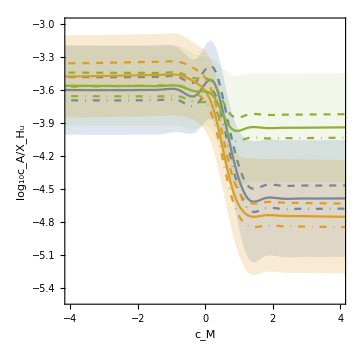

```mathematica
Show[
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,PlotRange->{{cmmin,cmmax},{-5.5,-3.0}},ImageSize->Medium,FrameLabel->{"c_M","log_10c_A/X_H_u"},AspectRatio->1,
PlotStyle->{colors[[1]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[1]]]
]& @ y12,
ListPlot[{{cMArray,#1[[1]]}//Transpose,{cMArray,#1[[3]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{{colors[[#2]],Dashed},{colors[[#2]],DotDashed}}
]&[y12vDelta,1],
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[2]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[2]]]
]& @ y13,
ListPlot[{{cMArray,#1[[1]]}//Transpose,{cMArray,#1[[3]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{{colors[[#2]],Dashed},{colors[[#2]],DotDashed}}
]&[y13vDelta,2],
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[3]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.1],colors[[3]]]
]& @ y23,
ListPlot[{{cMArray,#1[[1]]}//Transpose,{cMArray,#1[[3]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{{colors[[#2]],Dashed},{colors[[#2]],DotDashed}}
]&[y23vDelta,3]
]
```

```mathematica
Export["Figures/lepton_nh_cA.pdf",%]
```

Figures/lepton_nh_cA.pdf

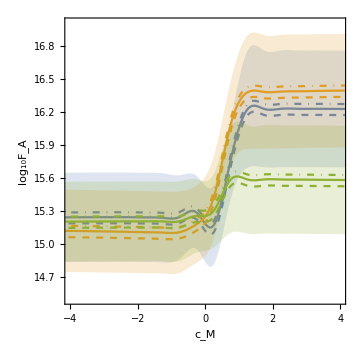

```mathematica
With[{σ0 =0.1,g=1,Mpl=1.22 10^19,zir=10^8,Δ=ΔArray[[2]]},
Clear[Fa];Fa[Δ_]:=Mpl/zir σ0/Sqrt[Δ-1];
Show[
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotRange->{{cmmin,cmmax},{14.5,17}},ImageSize->Medium,FrameLabel->{"c_M","log_10F_A"},AspectRatio->1,
PlotStyle->{colors[[1]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[1]]]
]& @ ( ({Log10[Fa[Δ]/(g^2 σ0^2)],0}-#)&/@y12),
ListPlot[{cMArray,#1[[1]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],Dashed}
]&[ (Log10[Fa[ΔArray[[1]]]/(g^2 σ0^2)]-y12vDelta),1],
ListPlot[{cMArray,#1[[3]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],DotDashed}
]&[ (Log10[Fa[ΔArray[[3]]]/(g^2 σ0^2)]-y12vDelta),1],
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[2]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[2]]]
]& @  ( ({Log10[Fa[Δ]/(g^2 σ0^2)],0}-#)&/@y13),
ListPlot[{cMArray,#1[[1]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],Dashed}
]&[ (Log10[Fa[ΔArray[[1]]]/(g^2 σ0^2)]-y13vDelta),2],
ListPlot[{cMArray,#1[[3]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],DotDashed}
]&[ (Log10[Fa[ΔArray[[3]]]/(g^2 σ0^2)]-y13vDelta),2],
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[3]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[3]]]
]& @ ( ({Log10[Fa[Δ]/(g^2 σ0^2)],0}-#)&/@y23),
ListPlot[{cMArray,#1[[1]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],Dashed}
]&[ (Log10[Fa[ΔArray[[1]]]/(g^2 σ0^2)]-y23vDelta),3],
ListPlot[{cMArray,#1[[3]]}//Transpose,
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[#2]],DotDashed}
]&[ (Log10[Fa[ΔArray[[3]]]/(g^2 σ0^2)]-y23vDelta),3],
ListPlot[Table[{i,12},{i,cMArray}],Joined->True,PlotStyle->{Opacity[0.2],colors[[5]]},
Filling->Bottom,FillingStyle->Directive[Opacity[0.2],colors[[5]]]]
]
]
```

```mathematica
Export["Figures/lepton_nh_FA.pdf",%]
```

Figures/lepton_nh_FA.pdf